2

ArcCos[e]

8 π (1+(e^2 Log[(1+√(1-e^2))/e])/(√(1-e^2)))

2 e^(1/3)

16 e^(2/3) π

(1+(e^2 Log[(1+√(1-e^2))/e])/(√(1-e^2)))/(2 e^(2/3))

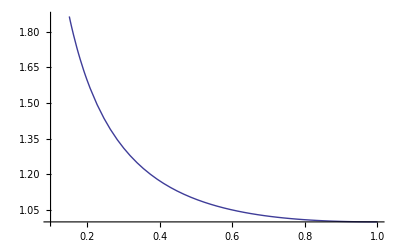

1.005 0.847461

1.01 0.792303

1.015 0.752789

1.02 0.721243

1.025 0.694714

1.03 0.671699

1.035 0.651311

1.04 0.632976

1.045 0.616298

1.05 0.60099

1.055 0.586837

1.06 0.573674

1.065 0.561369

1.07 0.549817

1.075 0.538931

1.08 0.528639

1.085 0.51888

1.09 0.509603

1.095 0.500765

1.1 0.492327

1.105 0.484255

1.11 0.476521

1.115 0.469099

1.12 0.461966

1.125 0.455101

1.13 0.448487

1.135 0.442107

1.14 0.435946

1.145 0.429991

1.15 0.424229

1.155 0.41865

1.16 0.413243

1.165 0.407999

1.17 0.402909

1.175 0.397965

1.18 0.39316

1.185 0.388487

1.19 0.38394

1.195 0.379513

1.2 0.3752

1.005 {e→0.847461}

1.01 {e→0.792303}

1.015 {e→0.752789}

1.02 {e→0.721243}

1.025 {e→0.694714}

1.03 {e→0.671699}

1.035 {e→0.651311}

1.04 {e→0.632976}

1.045 {e→0.616298}

1.05 {e→0.60099}

1.055 {e→0.586837}

1.06 {e→0.573674}

1.065 {e→0.561369}

1.07 {e→0.549817}

1.075 {e→0.538931}

1.08 {e→0.528639}

1.085 {e→0.51888}

1.09 {e→0.509603}

1.095 {e→0.500765}

1.1 {e→0.492327}

1.105 {e→0.484255}

1.11 {e→0.476521}

1.115 {e→0.469099}

1.12 {e→0.461966}

1.125 {e→0.455101}

1.13 {e→0.448487}

1.135 {e→0.442107}

1.14 {e→0.435946}

1.145 {e→0.429991}

1.15 {e→0.424229}

1.155 {e→0.41865}

1.16 {e→0.413243}

1.165 {e→0.407999}

1.17 {e→0.402909}

1.175 {e→0.397965}

1.18 {e→0.39316}

1.185 {e→0.388487}

1.19 {e→0.38394}

1.195 {e→0.379513}

1.2 {e→0.3752}

```mathematica
(* Finding the map between asphericity and aspect ratio *)
(* Oblate Spheroids a=b > c , e=c/a *)

a=2 (*doesnt depend on this *)
ae=ArcCos[e]
s= 2 π a^2( 1 + e^2/Sin[ae]Log[(1+Sin[ae])/Cos[ae]])
r=a *e^(1/3)  (* radius of a sphere with same volume *)
s0=4 π r^2
s=s/s0 (* asphericity *)
Plot[s,{e,0.1,1}]

For[i=1.005,i<=1.2,i+=0.005,Print[i," ",FindRoot[s==i, {e,0.1}]⟦1⟧⟦2⟧]]
```

2

ArcCos[1/e]

8 π (1+(e ArcCos[1/e])/(√(1-1/e^2)))

2 e^(1/3)

16 e^(2/3) π

(1+(e ArcCos[1/e])/(√(1-1/e^2)))/(2 e^(2/3))

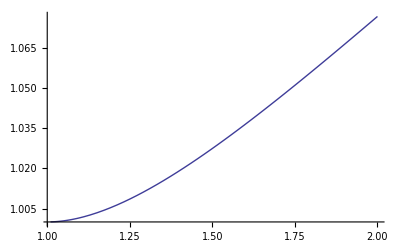

```mathematica
(* Prolate Spheroids a=b < c , e=c/a *)

a=2 (*doesnt depend on this *)
ae=ArcCos[1/e]
s= 2 π a^2( 1 + e ae/Sin[ae])
r=a *e^(1/3)  (* radius of a sphere with same volume *)
s0=4 π r^2
s=s/s0 (* asphericity *)
Plot[s,{e,1.01,2}]

ii=0;
map=Table[{0,0},{j,1,100}];

For[i=1.005,i<=1.2,i+=0.005,
ii=ii+1;
map⟦ii,1⟧=i;

map⟦ii,2⟧=FindRoot[s==i, {e,1.1}]⟦1⟧⟦2⟧;
]
```